```mathematica
(*///////////////////////////////Задание 2////////////////////////////////////////*)
ClearAll[p,rw];

p[r_]=DSolve[{D[r D[ p[r],r],r]==0,p'[rw]==1/(rw Log[rw]),p[1]==1},p,r][[1,1,2,2]]//Simplify
dp[r_]=D[p[r],r]
```

1+Log[r]/Log[rw]

1/(r Log[rw])

```mathematica
tetta=(dp[r0] (r1-r0))/(p[r1]-p[r0])//Simplify
```

(r0-r1)/(r0 Log[r0]-r0 Log[r1])

```mathematica
tetta/.r0->0.001/.r1->0.1009
```

21.6509

```mathematica
ClearAll[p]
p[r_]=DSolve[{D[r D[ p[r],r],r]==0,p'[rw]==-Q,p[1]==1},p,r][[1,1,2,2]]
```

1-Q rw Log[r]

```mathematica
ClearAll[p1,p2,rw];
(*rw=0.001;
k1=1;
k2=0.1;
x=0.5;*)
p=DSolve[{ D[r  k1 D[ p1[r],r],r]==0, D[r k2 D[p2[r],r],r]==0,p1[rw]==0,p2[1]==1,p1[x]==p2[x],k1 p1'[x]==k2 p2'[x]},{p1,p2},r]
```

{{p1→Function[{r},(-k2 Log[r]+k2 Log[rw])/(k2 Log[rw]+k1 Log[x]-k2 Log[x])],p2→Function[{r},(-k1 Log[r]+k2 Log[rw]+k1 Log[x]-k2 Log[x])/(k2 Log[rw]+k1 Log[x]-k2 Log[x])]}}

```mathematica
p1[r_]=p[[1,1,2,2]]//Simplify
p2[r_]=p[[1,2,2,2]]//Simplify
```

0.525461+0.0760683 Log[r]

1.+0.760683 Log[r]

```mathematica
p1[0.01]
```

0.175154

```mathematica
(*k11=1;*)
x=0.75;
p2=DSolve[{ D[r  k1 D[ p11[r],r],r]==0, D[r k12 D[p12[r],r],r]==0,p11[rw]==0,p12[1]==1,p11[x]==p12[x],k1 p11'[x]==k12 p12'[x]},{p11,p12},r]
```

{{p11→Function[{r},(0.151056 (6.90776 k12+1. k12 Log[r]))/(0.043456+1. k12)],p12→Function[{r},(1. (0.043456+1. k12+0.151056 Log[r]))/(0.043456+1. k12)]}}

```mathematica
P1[r_]=p2[[1,1,2,2]]
P2[r_]=p2[[1,2,2,2]]
```

(0.151056 (6.90776 k12+1. k12 Log[r]))/(0.043456+1. k12)

(1. (0.043456+1. k12+0.151056 Log[r]))/(0.043456+1. k12)

```mathematica
NSolve[P1'[rw]==p1'[rw],k12]
```

{{k12→0.0440824}}

0.0440824

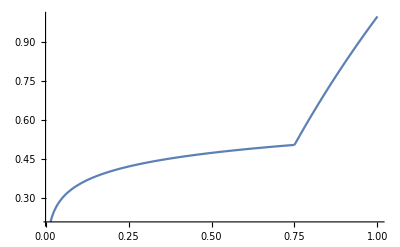

```mathematica
k12=0.04408240533408754
Show[Plot[P1[r]/.k12->0.04408240533408754,{r,0.001,0.75}],Plot[P2[r]/.k12->0.04408240533408754,{r,0.75,1}],PlotRange->All]
```

```mathematica
(*///////////////////////////////Задание 1////////////////////////////////////////*)
```

```mathematica
p=DSolve[{ D[ k1 D[ p1[r],r],r]==0, D[k2 D[p2[r],r],r]==0,p1[rw]==1,p2[1]==0,p1[x]==p2[x],k1 p1'[x]==k2 p2'[x]},{p1,p2},r]
```

{{p1→Function[{r},(-k1+k2 r+k1 x-k2 x)/(-k1+k2 rw+k1 x-k2 x)],p2→Function[{r},(-k1+k1 r)/(-k1+k2 rw+k1 x-k2 x)]}}

```mathematica
(*rw=0.01;
k1=1;
k2=0.1;
x=0.5;*)
p1[r_]=p[[1,1,2,2]]//Simplify
p2[r_]=p[[1,2,2,2]]//Simplify
```

(k1-k2 r-k1 x+k2 x)/(k1-k2 rw-k1 x+k2 x)

(k1 (-1+r))/(k2 (rw-x)+k1 (-1+x))

```mathematica
(*x=0.75;*)
p2=DSolve[{ D[k1 D[ p11[r],r],r]==0, D[k12 D[p12[r],r],r]==0,p11[rw]==1,p12[1]==0,p11[y]==p12[y],k1 p11'[y]==k12 p12'[y]},{p11,p12},r]
```

{{p11→Function[{r},(-k1+k12 r+k1 y-k12 y)/(-k1+k12 rw+k1 y-k12 y)],p12→Function[{r},(-k1+k1 r)/(-k1+k12 rw+k1 y-k12 y)]}}

```mathematica
P1[r_]=p2[[1,1,2,2]]
P2[r_]=p2[[1,2,2,2]]
NSolve[P1'[rw]==p1'[rw],k12]
```

(-k1+k12 r+k1 y-k12 y)/(-k1+k12 rw+k1 y-k12 y)

(-k1+k1 r)/(-k1+k12 rw+k1 y-k12 y)

{{k12→(k1 k2 (-1.+y))/(-1. k1+k1 x-1. k2 x+k2 y)}}

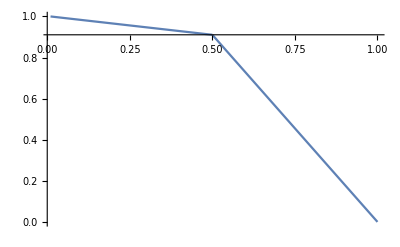

```mathematica
Show[Plot[p1[r],{r,rw,x}],Plot[p2[r],{r,x,1}],PlotRange->All]
```